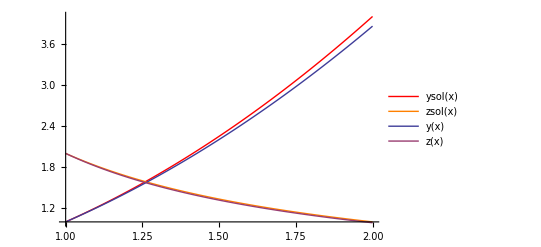

```mathematica
(*Зададим правые части системы дифференциальных уравнений*)
f1[x_,y_,z_]=y*z;
f2[x_,y_,z_]=-z^2+z/x;
(*Зададим начальные условия*)
x0=1;
Y={1};
Z={2};
(*Зададим правй конец отрезка*)
b=2;
(*Зададим количество частичных отрезков*)
n=20;
(*Найдем шаг разбиения*)
h=(b-x0)/n;
(*Построим разбиение отрезка на частичные*)
X=Table[x0+k*h,{k,0,n}];
(*Реализуем алгоритм метода Эйлера для решения задачи Коши для систем обыкновенных дифференциальных уравнений*)
For[k=1,k≤n,k++,
AppendTo[Y,Y[[k]]+h*f1[X[[k]],Y[[k]],Z[[k]]]];
AppendTo[Z,Z[[k]]+h*f2[X[[k]],Y[[k]],Z[[k]]]]
];
(*Выполним интерполяцию найденного приближенного решения многочленом Лагранжа*)y[x_]=Sum[Y[[i]]*Product[(x-X[[j]])/(X[[i]]-X[[j]]),{j,1,i-1}]*Product[(x-X[[j]])/(X[[i]]-X[[j]]),{j,i+1,n+1}],{i,1,n+1}];
z[x_]=Sum[Z[[i]]*Product[(x-X[[j]])/(X[[i]]-X[[j]]),{j,1,i-1}]*Product[(x-X[[j]])/(X[[i]]-X[[j]]),{j,i+1,n+1}],{i,1,n+1}];
(*Найдем точное решение*)DSol=DSolve[{s'[x]==f1[x,s[x],t[x]],t'[x]==f2[x,s[x],t[x]],s[x0]==Y[[1]],t[x0]==Z[[1]]},{s[x],t[x]},x];
zsol[x_]=t[x]/.DSol[[1]];
ysol[x_]=s[x]/.DSol[[1]];
(*Построим графики найденного решения в одной системе координат*)
G=Plot[{ysol[x],zsol[x]},{x,x0,b},PlotStyle->{Red,Orange},PlotLegends->"Expressions"];
GL=Plot[{y[x],z[x]},{x,x0,b},PlotLegends->"Expressions"];
Show[G,GL]
```